```mathematica
imgRes= {256,256}; η=1/2;
1-ExampleData[{"TestImage", "ResolutionChart"}];
ImagePad[%, (1-η)/(2η)*{imgRes, imgRes}];
img = ImageResize[%, imgRes]
Dimensions@ImageData@img
```

-Graphics-

```mathematica
imgH = DiscreteHadamardTransform[ImageData@img]//Image
```

-Graphics-

```mathematica
imgH
```

```mathematica
imgReconstruction = DiscreteHadamardTransform[ImageData@imgH]//Image
```

-Graphics-

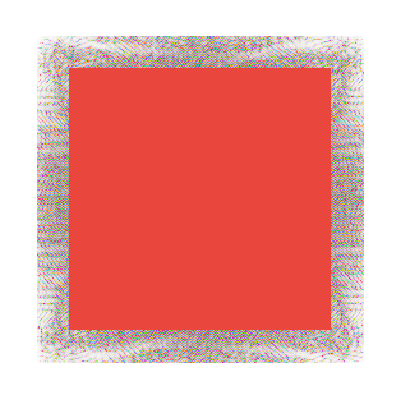

```mathematica
imgF = Fourier[ImageData@img];
x =Round[ 256/2*0.8];
imgF[[128-x;;128+x,128-x;;128+x]] = 0 ;
imgF// ComplexArrayPlot
```

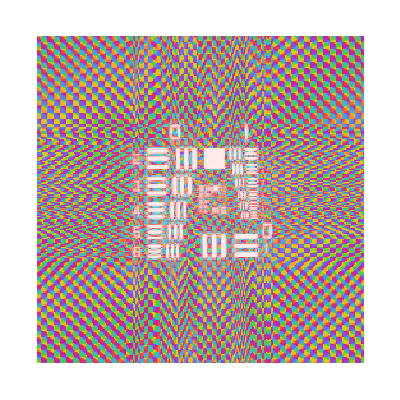

```mathematica
imageFR = InverseFourier[imgF]//ComplexArrayPlot
```